NALOGA 1

```mathematica
d=Daljica[{-1,1},{3,-1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
d2=Daljica[{-1,-1},{3,1}]
```

Daljica[{-1,-1},{3,1}]

```mathematica
d3=Daljica[{-1,2},{3,0}]
```

Daljica[{-1,2},{3,0}]

```mathematica
Dolžina[Daljica[AA_,BB_]]:=Norm[BB-AA]
```

```mathematica
Dolžina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]]:=Line[{AA,BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Nariši[d_Daljica]:=Graphics[Slika[d]]
```

```mathematica
Nariši[d__Daljica]:=Graphics[Map[Slika, List[d]]]
```

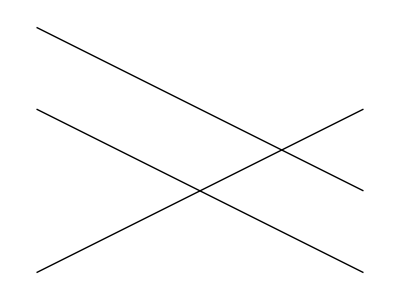

```mathematica
Nariši[d, d2, d3]
```

```mathematica
ClearAll[x,y]
```

```mathematica
EnačbaNosilke[Daljica[AA_,BB_]]:=Module[{x1,y1,x2,y2,k,n},
{x1,y1}=AA;
{x2,y2}=BB;

k=(y2-y1)/(x2-x1);
n=y1-(k*x1);
y==k*x+n
]
```

```mathematica
EnačbaNosilke[d]
```

y==1/2-x/2

```mathematica
y
```

y

NALOGA 2

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:=Module[{rešitev},
rešitev=Solve[{AA+r(BB-AA)==CC+s(DD-CC),r>=0,r≤1,s≥0, s≤1},{r,s}];
AA+r(BB-AA)/.rešitev//First
]
```

```mathematica
Presek[d,d2]
```

{1,0}

```mathematica
ClearAll[Presek,resitev]
```

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:=Module[{rešitev},
rešitev=Solve[{AA+r(BB-AA)==CC+s(DD-CC),r>=0,r≤1,s≥0, s≤1},{r,s}]

]
```

```mathematica
Presek[d,d3]
```

{}

```mathematica
ClearAll[Presek,resitev]
```

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:=Module[{rešitev},
rešitev=Solve[{AA+r(BB-AA)==CC+s(DD-CC),r>=0,r≤1,s≥0, s≤1},{r,s}];
If[rešitev =={},
{},
First[AA+r(BB-AA)/.rešitev]]]
```

```mathematica
Presek[d,d3]
```

{}

NALOGA 3

```mathematica
ClearAll[Slika]
```

```mathematica
m1= Mnogokotnik [{0,0},{1,1},{0,3},{-1,2}]
Slika[Mnogokotnik[t__]]:=Line[{t}]
Slika[Mnogokotnik[t__]]:=Line[{{0,0},{1,1},{0,3},{-1,2},First[m1]}]
Slika[m1]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

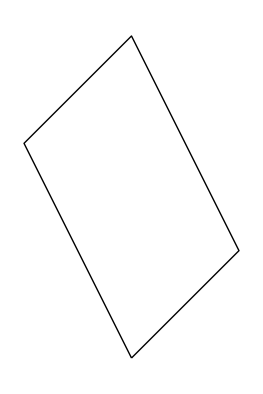

```mathematica
Nariši[m__Mnogokotnik]:=Graphics[Slika[m1]]
Nariši[m1]
```

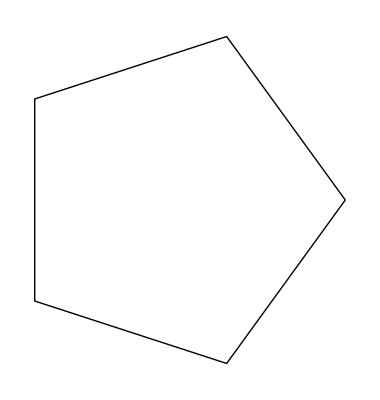

```mathematica
PravilniNKotnik[n_,r_]:= 
Graphics[{Line[Table[{r* Cos[(2Pi * i)/n],r*Sin[(2 Pi *i)/n]},{i,0,n}]]}]
PravilniNKotnik[5,2]
```

```mathematica
PravilniNKotnik[n_,r_,phi_] := Manipulate[Graphics[{Line[Table[{r*Cos[(2Pi*i+x)/n ],r*Sin[(2Pi*i+x)/n]},{i,0,n}]],Point[{0,0}]}],{x,0,Pi}]
PravilniNKotnik[5, 2, Pi]
```

```mathematica
Daljice[Mnogokotnik[t__]]:=Partition[{t},2,1]
Daljice[m1]
```

{{{0,0},{1,1}},{{1,1},{0,3}},{{0,3},{-1,2}}}

NALOGA 4

```mathematica
ClearAll[d,m1,AA,BB,CC,DD,EE,FF,r,s,dolžina, daljica, presek]
```

```mathematica
d={{-1,1},{3,-1}}
m1= {{0,0},{1,1},{0,3},{-1,2}}
```

{{-1,1},{3,-1}}

{{0,0},{1,1},{0,3},{-1,2}}

```mathematica
Dolžina[d[EE_,FF_]]:=Norm[FF-EE]
{d}
```

{{{-1,1},{3,-1}}}

```mathematica
Presek[m1[AA_,BB_,CC_ DD_],d[EE_,FF_]:=Module[{rešitev},
rešitev=Solve[{AA+r(BB-AA)+r(CC-BB)+r(DD-CC)==EE+s(FF-EE),r>=0,r≤1,s≥0, s≤1},{r,s}]]]
```

SetDelayed::write: Tag List in {{-1,1},{3,-1}}[EE_,FF_] is Protected.

Presek[{{0,0},{1,1},{0,3},{-1,2}}[AA_,BB_,CC_ DD_],$Failed]

```mathematica
Presek[m1,d]
```

Presek[m1,d]

NALOGA 5

```mathematica
ClearAll[f, a, b, d]
```

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
Outer[{1,2,3},{2,8,6},{4,5}]
```

{{{1,2,3}[2,4],{1,2,3}[2,5]},{{1,2,3}[8,4],{1,2,3}[8,5]},{{1,2,3}[6,4],{1,2,3}[6,5]}}

```mathematica
r=Outer[f,{1,2,3},{2,8,6},{4,5}]
```

{{{f[1,2,4],f[1,2,5]},{f[1,8,4],f[1,8,5]},{f[1,6,4],f[1,6,5]}},{{f[2,2,4],f[2,2,5]},{f[2,8,4],f[2,8,5]},{f[2,6,4],f[2,6,5]}},{{f[3,2,4],f[3,2,5]},{f[3,8,4],f[3,8,5]},{f[3,6,4],f[3,6,5]}}}

```mathematica
Flatten[r]
```

{f[1,2,4],f[1,2,5],f[1,8,4],f[1,8,5],f[1,6,4],f[1,6,5],f[2,2,4],f[2,2,5],f[2,8,4],f[2,8,5],f[2,6,4],f[2,6,5],f[3,2,4],f[3,2,5],f[3,8,4],f[3,8,5],f[3,6,4],f[3,6,5]}

```mathematica
Flatten[{{1,2,3},{2,8,6},{4,5}}]
```

{1,2,3,2,8,6,4,5}

```mathematica
ClearAll[VsiPari, f, sez1, sez2, m2,m1]
```

```mathematica
m1= {{0,0},{1,1},{0,3},{-1,2}}
```

{{0,0},{1,1},{0,3},{-1,2}}

```mathematica
m2={{1,-2},{1,8},{4,5},{3,6}}
```

{{1,-2},{1,8},{4,5},{3,6}}

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
```

```mathematica
Outer[f,m1,m2]
```

{{{{f[0,1],f[0,-2]},{f[0,1],f[0,8]},{f[0,4],f[0,5]},{f[0,3],f[0,6]}},{{f[0,1],f[0,-2]},{f[0,1],f[0,8]},{f[0,4],f[0,5]},{f[0,3],f[0,6]}}},{{{f[1,1],f[1,-2]},{f[1,1],f[1,8]},{f[1,4],f[1,5]},{f[1,3],f[1,6]}},{{f[1,1],f[1,-2]},{f[1,1],f[1,8]},{f[1,4],f[1,5]},{f[1,3],f[1,6]}}},{{{f[0,1],f[0,-2]},{f[0,1],f[0,8]},{f[0,4],f[0,5]},{f[0,3],f[0,6]}},{{f[3,1],f[3,-2]},{f[3,1],f[3,8]},{f[3,4],f[3,5]},{f[3,3],f[3,6]}}},{{{f[-1,1],f[-1,-2]},{f[-1,1],f[-1,8]},{f[-1,4],f[-1,5]},{f[-1,3],f[-1,6]}},{{f[2,1],f[2,-2]},{f[2,1],f[2,8]},{f[2,4],f[2,5]},{f[2,3],f[2,6]}}}}

```mathematica
Presek[m1_Mnogokotnik,m2_Mnogokotnik]:=Vsi pari[f,m1,m2]
```

```mathematica
Presek[m1,m2]
```

Presek[{{0,0},{1,1},{0,3},{-1,2}},{{1,-2},{1,8},{4,5},{3,6}}]

NALOGA 6

Izračunaj skalarni produkt dveh vektorjev, če imamo podane njune komponente A ( -1 , -6 , 3 ) in B ( 2 , 0 , 5 ).

```mathematica
v1 = {-1,-6,3}
v2={2,0,5}
```

{-1,-6,3}

{2,0,5}

```mathematica
v1.v2
```

13

```mathematica
Graphics3D[{Red,Arrow[{v1,v2}]},Axes->True,Boxed->True,AxesLabel->{x,y,z}]
```

-Graphics3D-